```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlibpub.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
```

```mathematica
(* Input parameters *)
model="nonlinear3d";
If[model=="linear",
	Ca=1/2;γ=1;Rey=Infinity;
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
	(*myeqn=rdd+rd+(r-ro)+Cp[t]==0;*)
	eqn=rdd+rd+(r-ro)==0;
	vars={{r,rd,ro},rdd};
	(*vars={{r,rd},rdd};*)
];
If[model=="nonlinear2d",
	γ=1.4;
	Cp0=1;
	Toneperiod=3.4  (1/Cp0)^0.75;
	Cp[t_]:=Cp0;
	(*Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];*)	
	ro=1;
	eqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
	vars={{r,rd},rdd};
];
If[model=="nonlinear3d",
	γ=1.4;
	Cp0=1;
	Toneperiod=3.4  (1/Cp0)^0.75;
	Cp[t_]:=Cp0;
	eqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
	vars={{r,rd,ro},rdd};
];
If[model=="firstorder",
	Cp0=1;
	Toneperiod=1;
	(*eqn=rd+r-r^2==2;*)
	eqn=rd==4r-2 r^2;
	vars={{r},rd};
	(*tmax=5;
	sol=First[rr[tt]/.NDSolve[{rr'[tt]==4rr[tt](*-1 rr[tt]^(-1/2)*)-2 rr[tt]^2,rr[0]==0.5},rr[tt],{tt,0,tmax}]]
	Plot[sol/.tt->t,{t,0,tmax},PlotRange->All]*)
];

dimensions=Length[vars[[1]]];
idx=Table[c[i],{i,dimensions}];
{coefs,exps}=TransportTerms[eqn,vars,idx];
```

```mathematica
Nperiod=5;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=10000dt;
tol=10 10^-6;

If[dimensions==1,
	n[1]=3;
	μR=0.5;σR=0.1;
	𝒟r=NormalDistribution[μR,σR];
	momRRd[idx_]:=Moment[𝒟r,idx[[1]]];
];
If[dimensions==2,
	n[1]=2;n[2]=2;
	perms={12};
	(*perms={12,21};*)
	nperm=Length[perms];
	
	μR=1.;σR=0.1;
	𝒟r=LogNormalDistribution[Log[μR],σR];
	μRd=0;σRd=Sqrt[0.05];
	𝒟v=NormalDistribution[μRd,σRd];		
	RRdPDF=ProductDistribution[𝒟r,𝒟v];
	momRRd[idx_]:=Moment[RRdPDF,idx];
];
If[dimensions==3,
	n[1]=2;n[2]=2;n[3]=3;
	perms={12};
	(*perms={12,21};*)
	nperm=Length[perms];
	
	μRo=1.;σRo=0.1;
	𝒟ro=LogNormalDistribution[Log[μRo],σRo];
	momRo[i_]:=Moment[𝒟ro,i];
	momRos=Table[momRo[i],{i,0,2n[3]-1}];
	{Ros,wRos}=Wheeler[momRos];
	(*Ros={1};wRos={1};*)
	μRd=0;σRd=Sqrt[0.05];
	𝒟v=NormalDistribution[μRd,σRd];
	Do[
		μR=Ros[[i]];σR=0.1;
		𝒟r[i]=LogNormalDistribution[Log[μR],σR];
		(*RRdPDF[i]=ProductDistribution[𝒟r[i],𝒟v];*)
		RRdPDF[i]=BinormalDistribution[{μR,μRd},{σR,σRd},0.1];
	,{i,n[3]}];
	momRRd[idx_]:=Moment[RRdPDF[idx[[3]]+1],{idx[[1]],idx[[2]]}];
	RRdRoPDF=ProductDistribution[𝒟r,𝒟v,𝒟ro];
];

method="CHYQMOM" ;(* Options: "QMOM", "HYQMOM", "CQMOM", "CHYQMOM"*)
ks=MomentIndex[n,method,nperm];
ksp={{3,0,0},{2,1,0},{3,2,0},{3(1-γ),0,3γ}};
```

```mathematica
getF[w_,xi_,t_,ks_]:=Module[
	{rhs,rule,myexps,mycoefs,rhstot},
	rhstot={};
	Do[
		rule=Flatten[{Table[c[i]->ks[[j,i]],{i,dimensions}],ttt->t}];
		myexps=Table[exps[[i]]/.rule,{i,Length[exps]}];
		mycoefs=Table[coefs[[i]]/.rule,{i,Length[coefs]}];
		If[dimensions==1||dimensions==2,
			rhs=Sum[mycoefs[[i]]Quadrature[w,xi,myexps[[i]]],{i,Length[coefs]}]
		];
		If[dimensions==3,
			rhs=Sum[
				mycoefs[[i]]pow[Ros[[ks[[j,3]]+1]],myexps[[i,3]]-ks[[j,3]]]
				Quadrature[w,xi,{myexps[[i,1]],myexps[[i,2]],1+ks[[j,3]]}]
			,{i,Length[coefs]}];
		];
		AppendTo[rhstot,rhs];
	,{j,Length[ks]}];
	Return[rhstot,Module];
];

F[moms_,t_]:=Module[{rhs,mom,mout,rout},
	Do[
		{w,xi}=MomentInvert[moms,ks,Method->method,Permutation->perms[[i]]];
		rhs[i]=getF[w,xi,t,ks];
		mom[i]=Project[w,xi,ks];
	,{i,nperm}];
	mout=Sum[mom[i],{i,nperm}]/nperm;
	rout=Sum[rhs[i],{i,nperm}]/nperm;
	Return[{mout,rout},Module];
];

TotalMoments[moms_,idx_]:=Sum[wRos[[l]] Ros[[l]]^idx[[3]] MomentFind[moms,ks,{idx[[1]],idx[[2]],l-1}],{l,n[3]}];
```

```mathematica
(* ic *)moms=Table[momRRd[ks[[i]]],{i,Length[ks]}];

sol={};ts={};dets={};abscissa={};fullmoms={};
t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,F,t,dt];
	AppendTo[sol,moms];AppendTo[ts,t];
	If[dimensions==1,AppendTo[abscissa,Re[Flatten[xi]]]];
	If[dimensions==2,AppendTo[abscissa,Thread[xi]]];
	If[dimensions==3,
		AppendTo[abscissa,Table[Thread[{xi[[1]][j],xi[[2]][j]}],{j,n[3]}]];
		fullmom=Table[TotalMoments[moms,ks[[i]]],{i,Length[ks]}];
		AppendTo[fullmoms,fullmom];
	];

	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^5,Print["Crash ",100 t/T];Break[]];
	(*If[e<10^-16&&t>0.1T,Print["Error zero, stationary point likely reached. Aborting."];Break[]];*)
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]},{t,T}}]
]//AbsoluteTiming
Length[ts]
```

{11.5787,Null}

480

```mathematica
myn=100;
plottingfac=1;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
Do[myabscissa[j]=Table[abscissa[[i,j]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}],{j,nro}];
Do[
	xdat[j]=myabscissa[j][[All,All,1]];
	ydat[j]=myabscissa[j][[All,All,2]];
	xmax[j]=If[Max[xdat[j]]>0,1.2 Max[xdat[j]],0.8 Max[xdat[j]]];
	xmin[j]=If[Min[xdat[j]]<0,1.2 Min[xdat[j]],0.8 Min[xdat[j]]];
	ymax[j]=If[Max[ydat[j]]>0,1.2 Max[ydat[j]],0.8 Max[xdat[j]]];
	ymin[j]=If[Min[ydat[j]]<0,1.2Min[ydat[j]],0.8 Min[ydat[j]]];
,{j,nro}];
xminF=Min[Table[xmin[j],{j,nro}]];
xmaxF=Max[Table[xmax[j],{j,nro}]];
yminF=Min[Table[ymin[j],{j,nro}]];
ymaxF=Max[Table[ymax[j],{j,nro}]];

dat3d=Table[Flatten[Table[Table[Flatten[{Ros[[j]],myabscissa[j][[k,i]]},1],{i,Length[myabscissa[j][[k]]]}],{j,nro}],1],{k,Length[myabscissa[1]]}];
```

```mathematica
ListAnimate[ParallelTable[
ListPlot[
	Table[myabscissa[j][[i]],{j,nro}],PlotRange->{{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},AxesLabel->{"R","V"}]
,{i,1,Length[myabscissa[1]]/plottingfac}]]
```

```mathematica
anim=ListAnimate[
	ParallelTable[
		ListPointPlot3D[dat3d[[i]],PlotRange->{{0.9Min[Ros],1.1Max[Ros]},{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},
			AxesLabel->{"Ro","R","V"}]
	,{i,Length[dat3d]/plottingfac}]
]
(*Export["~/Desktop/anim2.avi",anim,AnimationRunTime->6];*)
```

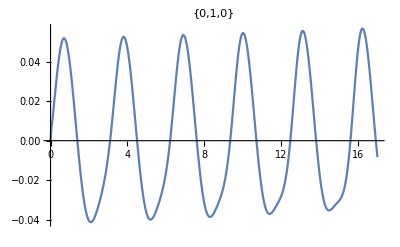
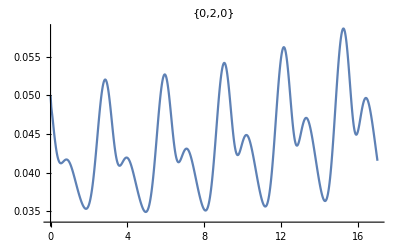
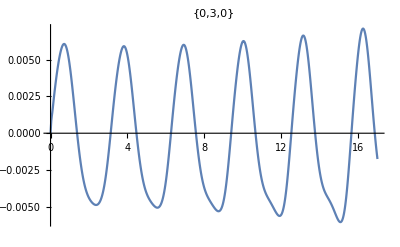
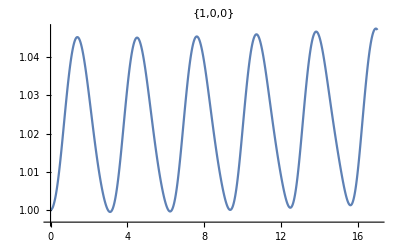
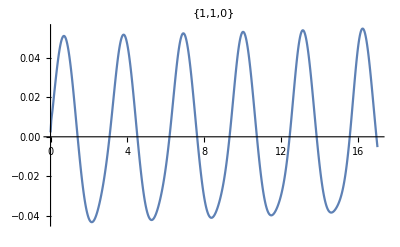
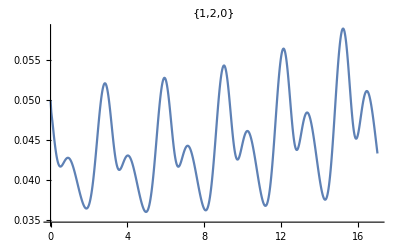
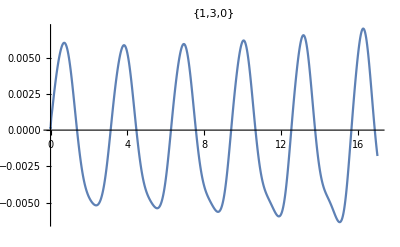
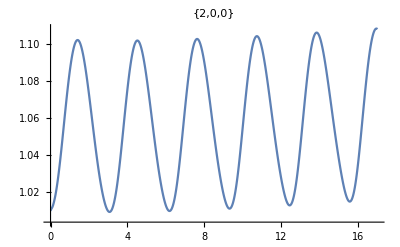

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,fullmoms[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
If[
	dimensions==3,
	NcasesRRd=50;
	cases=RandomVariate[RRdRoPDF,Ncases];

	NcasesRo=50;
	casesRo=RandomVariate[𝒟ro,NcasesRo]//Sort;
	Do[casesRRd[i]=RandomVariate[ProductDistribution[LogNormalDistribution[Log[casesRo[[i]]],σR],𝒟v],NcasesRRd],{i,NcasesRo}];
	cases=Flatten[Table[{casesRRd[kk][[i,1]],casesRRd[kk][[i,2]],casesRo[[kk]]},{i,NcasesRRd},{kk,NcasesRo}],1];
	Ncases=Length[cases];
,
	Ncases=3000;
	cases=RandomVariate[RRdPDF,Ncases];
	cases=Table[{cases[[i,1]],cases[[i,2]],ro},{i,Ncases}];
];

Clear[t];
If[model=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
If[model=="nonlinear",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(cases[[i,3]]/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
mydr=ParallelTable[D[myr[[i]],t],{i,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[
	Table[
	{
	myr[[j]]/.{t->ts2[[i]]},
	mydr[[j]]/.{t->ts2[[i]]},
	cases[[j,3]]
	}
	,{j,Ncases}]
,{i,Nt}];

mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;3]]]},{i,Nt}],{j,Length[ks]}];
mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;3]]]},{i,Nt}],{j,Length[ksp]}];
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]/1}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/movie.avi",vid]*)
```

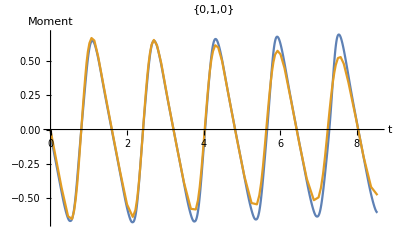
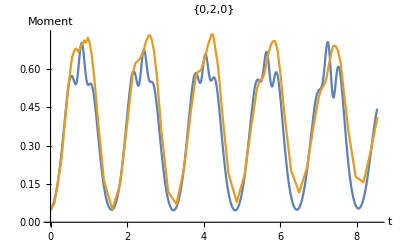
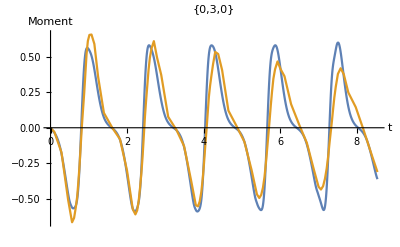
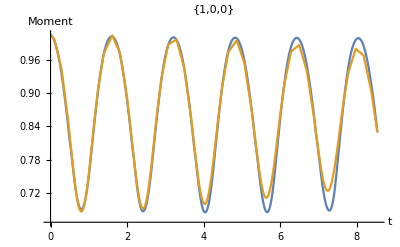
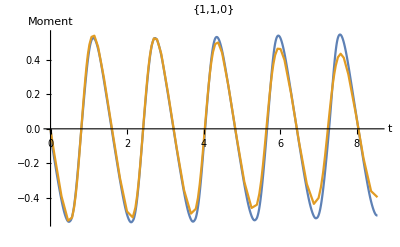
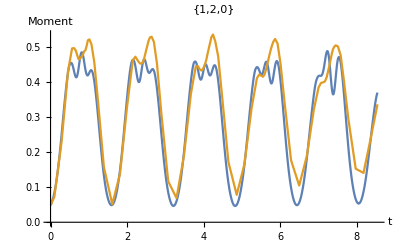
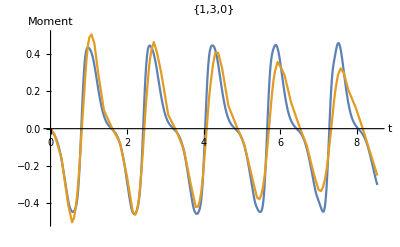
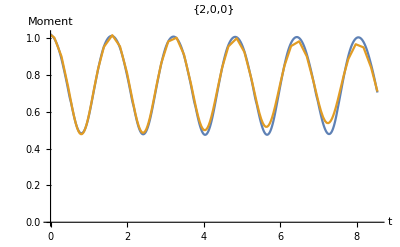

{}

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,fullmoms[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
,{i,1,Length[momsp]}]
plots
```